```mathematica
Exit[];
```

```mathematica
$Assumptions=  r>0 && Element[m,Integers] && Element[n,Integers]  && s>0
```

r>0&&m∈Integers&&n∈Integers&&s>0

# 2-d Dirac

```mathematica
f1[r_,En_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}};f1[r,En]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^p)
ⅈ (En-r^p) | -m/r)

# Diagonaldarstellung für r gegen Infinity

```mathematica
V={{1,1},{-1,1}};Simplify[V.f1[r,En].Inverse[V]]//MatrixForm
```

(ⅈ En-1/(2 r)-ⅈ r^p | (1-2 m)/(2 r)
(1-2 m)/(2 r) | -ⅈ En-1/(2 r)+ⅈ r^p)

```mathematica
Inverse[V].{0,C}
```

{-C/2,C/2}

# Potenzreihenansatz mit richtigem Rangverhalten

# m>=1

```mathematica
s=m-1;p=.;
```

```mathematica
f1[r,En]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^p)
ⅈ (En-r^p) | -m/r)

```mathematica
u={F[x],G[x]}*x^(s)
```

{x^(-1+m) F[x],x^(-1+m) G[x]}

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f1[r[x],En].u)/x^(s-0)]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{(ⅈ En-ⅈ x^p) G[x]-F'[x],(ⅈ En-ⅈ x^p) F[x]+(1/x-(2 m)/x) G[x]-G'[x]}

```mathematica
m=.;
```

```mathematica
f2[x_,En_]:={{0,(ⅈ En-ⅈ x^p) },{(ⅈ En-ⅈ x^p),(1/x-(2 m)/x) }};f2[r,En]//MatrixForm
```

(0 | ⅈ En-ⅈ r^p
ⅈ En-ⅈ r^p | 1/r-(2 m)/r)

```mathematica
u={F[x],G[x]}*Exp[I*(x^(p+1)/(p+1)-x*En)]
```

{ⅇ^(ⅈ (-En x+x^(1+p)/(1+p))) F[x],ⅇ^(ⅈ (-En x+x^(1+p)/(1+p))) G[x]}

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f2[r[x],En].u)/Exp[I*(x^(p+1)/(p+1)-x*En)]]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{(ⅈ En-ⅈ x^p) F[x]+(ⅈ En-ⅈ x^p) G[x]-F'[x],(ⅈ En-ⅈ x^p) F[x]+(ⅈ En+1/x-(2 m)/x-ⅈ x^p) G[x]-G'[x]}

```mathematica
f[x_,En_]:={{(ⅈ En-ⅈ x^p) ,(ⅈ En-ⅈ x^p) },{(ⅈ En-ⅈ x^p),(ⅈ En+1/x-(2 m)/x-ⅈ x^p) }};f[r,En]//MatrixForm
```

(ⅈ En-ⅈ r^2 | ⅈ En-ⅈ r^2
ⅈ En-ⅈ r^2 | ⅈ En+1/r-(2 m)/r-ⅈ r^2)

```mathematica
u={a[n],b[n]}*x^n
```

{x^n a[n],x^n b[n]}

```mathematica
p=2;
```

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f[r[x],En].u)*x]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{x^n ((-n+ⅈ En x-ⅈ x^3) a[n]+(ⅈ En x-ⅈ x^3) b[n]),x^n ((ⅈ En x-ⅈ x^3) a[n]+(1-2 m-n+ⅈ En x-ⅈ x^3) b[n])}

```mathematica
g2=Table[Simplify[Sum[D[g1,{x,n2}]/n2!,{n,0,7}]/.x->0],{n2,0,7}];g2//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
a[0]=1;b[0]=0; a[1]=I*En;a[2]=I En  (a[1]+b[1])/2;
```

```mathematica
a[1]=.;a[2]=.;b[1]=.;b[0]=.;a[0]=.;b[2]=.;a[n_]=.;b[n_]=.;
```

Unset::norep: Assignment on b for b[1] not found.

Unset::norep: Assignment on b for b[2] not found.

```mathematica
b[n_]:=n/(-1+2 m+n)a[n];
```

```mathematica
a[n_]:=ⅈ (En a[n-1] (2 m -1 +2 (n-1))/(n(2 m-1+(n-1)))-a[n-3](2m-1+2(n-3))/(n(2m-1+(n-3))))
```

```mathematica
Un[Ene_,mm_,nN_,x_]:=Module[{n,U1,U2,U3,U4,Erg,T},
U1=1;U2=I*Ene;U3=1/2 ⅈ Ene (ⅈ Ene+(ⅈ Ene)/(2 mm));
Erg={U1,0}+U2*{1,1/(-1+2 mm+1)}*x+U3*{1,2/(-1+2 mm+2)}*x^2;
For[n=3,n≤nN,n++,
U4=ⅈ (Ene U3(2 mm -1 +2 (n-1))/(n(2 mm-1+(n-1)))-U1(2mm-1+2(n-3))/(n(2mm-1+(n-3))));
U1=U2;U2=U3;U3=U4;
Erg+=U3*x^n*{1,n/(-1+2 mm+n)};

];

Erg]
```

```mathematica
UnD[Enne_,mm_,nN_,x_]:=Module[{Ene,n,U1,U2,U3,U4,Erg,T},
U1=1;U2=I*Ene;U3=1/2 ⅈ Ene (ⅈ Ene+(ⅈ Ene)/(2 mm));
Erg=D[{U1,0}+U2*{1,1/(-1+2 mm+1)}*x+U3*{1,2/(-1+2 mm+2)}*x^2,Ene]/.Ene->Enne;
For[n=3,n≤nN,n++,
U4=ⅈ (Ene U3(2 mm -1 +2 (n-1))/(n(2 mm-1+(n-1)))-U1(2mm-1+2(n-3))/(n(2mm-1+(n-3))));
U1=U2;U2=U3;U3=U4;
Erg+=D[U3*x^n*{1,n/(-1+2 mm+n)},Ene]/.Ene->Enne;

];

Erg]
```

# zur Probe

```mathematica
Uno[Ene_,m_,nN_,x_]:=Module[{n,U,Erg=0},
U={{a[0],b[0]}};
For[n=1,n≤nN+1,n++,
AppendTo[U,{a[n],b[n]}]
];
For[n=0,n≤nN,n++,
Erg+=U[[n+1]]*x^n;
];
Erg
]
```

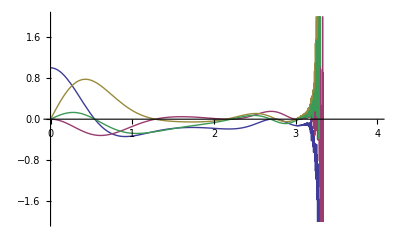

```mathematica
Ge={Re[#],Im[#]}&[Un[3,2,250,x]];Plot[Ge,{x,0,4},PlotRange->{-2,2}]
```

```mathematica
Analytische Lösung an stelle x mit güte g
```

```mathematica
U[Ene_,mm_,g_,x_]:=Module[{n=2,U1,U2,U3,U4,Erg,T},
U1=1;U2=I*Ene;U3=1/2 ⅈ Ene (ⅈ Ene+(ⅈ Ene)/(2 mm));
Erg={U1,0}+U2*{1,1/(-1+2 mm+1)}*x+U3*{1,2/(-1+2 mm+2)}*x^2;
While[Abs[U3*x^n]>g,n++;
U4=ⅈ (Ene U3(2 mm -1 +2 (n-1))/(n(2 mm-1+(n-1)))-U1(2mm-1+2(n-3))/(n(2mm-1+(n-3))))//N;
U1=U2;U2=U3;U3=U4;
Erg+=U3*x^n*{1,n/(-1+2 mm+n)};

];

{Erg,n}]
```

```mathematica
U[5.533021207627789+0.2865166733657229 ⅈ,2,10^-10,1]
```

{{-0.0446669+0.0833148 ⅈ,0.00763192-0.0254178 ⅈ},59}

# Berechnung der Eigenwerte

```mathematica
m=2;En=.
```

```mathematica
u={F[x],G[x]}*{ⅇ^(-2 ⅈ (-En x+x^(1+p)/(1+p))),1}
```

{ⅇ^(-2 ⅈ (-En x+x^3/3)) F[x],G[x]}

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*V.f[r[x],En].Inverse[V].u)*{ⅇ^(2 ⅈ (-En x+x^(1+p)/(1+p))),1}]]],{F[x],G[x]}];
g1
```

{-(3 F[x])/(2 x)-(3 ⅇ^(2/3 ⅈ x (-3 En+x^2)) G[x])/(2 x)-F'[x],-(3 ⅇ^(-2/3 ⅈ x (-3 En+x^2)) F[x])/(2 x)-(3 G[x])/(2 x)-G'[x]}

```mathematica
f3[x_,En_]={{-3/(2 x),-(3 ⅇ^(2/3 ⅈ x (-3 En+x^2)))/(2 x)},{-(3 ⅇ^(-2/3 ⅈ x (-3 En+x^2)))/(2 x),-3/(2 x)}};f3[x,En]//MatrixForm
```

(-3/(2 x) | -(3 ⅇ^(2/3 ⅈ x (-3 En+x^2)))/(2 x)
-(3 ⅇ^(-2/3 ⅈ x (-3 En+x^2)))/(2 x) | -3/(2 x))

```mathematica
f3[x_,En_]={{(-3/(2 x)-2 ⅈ x^2) ,-(3 ⅇ^(-2 ⅈ En x))/(2 x)},{-(3 ⅇ^(2 ⅈ En x))/(2 x),-3/(2 x)}};f3[x,En]//MatrixForm
```

(-3/(2 x)-2 ⅈ x^2 | -(3 ⅇ^(-2 ⅈ En x))/(2 x)
-(3 ⅇ^(2 ⅈ En x))/(2 x) | -3/(2 x))

```mathematica
fE[x_,En_]=D[f3[x,En],En]
```

{{0,3 ⅈ ⅇ^(2/3 ⅈ x (-3 En+x^2))},{-3 ⅈ ⅇ^(-2/3 ⅈ x (-3 En+x^2)),0}}

76

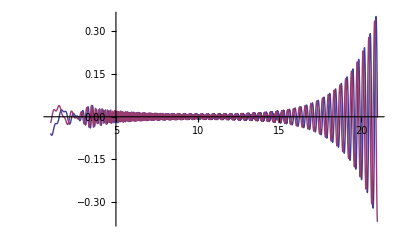

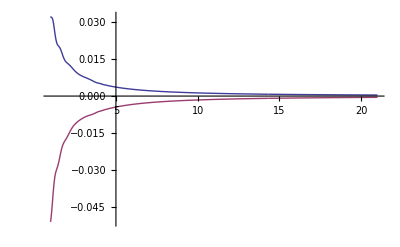

```mathematica
nn=12000;S=1;h=20/nn;ra=1;m=2;r=1;p=2;En=8.880855682072815+0.37429193692418034 ⅈ;
NN=U[En,m,10^-10,r];NN[[2]]
k=(V.NN[[1]])*{ⅇ^(2 ⅈ (-En x)),1}/.x->r;
kK={{r,k}};
Do[
k0=h*f3[r,En].k;k1=h*f3[r+h/2,En].(k+k0/2);k2=h*f3[r+h/2,En].(k+k1/2);k3=h*f3[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);
r+=h;

AppendTo[kK,{r,k}],{nn}];

ListPlot[Join[{ {#[[1]],Re[#[[2,1]] ]}&/@kK[[S;;nn]]//N},{ {#[[1]],Im[#[[2,1]] ]}&/@kK[[S;;nn]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;nn]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;nn]]//N}],PlotRange->All,Joined->True]
r=.;En=.;
```

```mathematica
k
```

{0.00465272-0.00479282 ⅈ,0.000410979-0.000519741 ⅈ}

```mathematica
nn=6000;S=1;h=20/nn;ra=1;m=2;r=1;p=2;
NN=U[En,m,10^-10,r];NN[[2]]
k=(V.NN[[1]])*{ⅇ^(2 ⅈ (-En x)),1}/.x->r;
kK={{r,k}};

Do[
k0=h*f3[r,En].k;k1=h*f3[r+h/2,En].(k+k0/2);k2=h*f3[r+h/2,En].(k+k1/2);k3=h*f3[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);

k0=h*(fE[r,En].k+f3[r,En].kE);k1=h*(fE[r,En].k+f3[r+h/2,En].(kE+k0/2));k2=h*(fE[r,En].k+f3[r+h/2,En].(kE+k1/2));k3=h*(fE[r,En].k+f3[r+h,En].(kE+k2));
kE+=1/6*(k0+2*k1+2*k2+k3);

r+=h;
,{nn}];

r=.;
k[[1]]
En-=k[[1]]/kE[[1]]
```

76

0.30809-0.459975 ⅈ

8.88086+0.374292 ⅈ

```mathematica
En=8.861374393073042+0.27884769664485737 ⅈ;
```

```mathematica
S=nn-Pi/Re[En]/h;ListPlot[Join[{ {#[[1]],Re[#[[2,1]] ]}&/@kK[[S;;nn]]//N},{ {#[[1]],Im[#[[2,1]]]}&/@kK[[S;;nn]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[Cos[ Re[En] #[[1]]]]}&/@kK[[S;;nn]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;nn]]//N}],PlotRange->All,Joined->True]
```

Part::span: 12000 - 600\ π/Re[En] ;; 12000 is not a valid Span specification.  A Span specification should be 1, 2, or 3 integers separated by ;;.  (Any of the integers can be omitted, or replaced with All.)

Part::partd: Part specification (12000 - 600\ π/Re[En] ;; 12000) ⟦ 2, 1 ⟧ is longer than depth of object.

Part::pspec: Part specification {12000 - 600\ π/Re[En], Re[(12000 - 600\ π/Re[« 1 »] ;; 12000) ⟦ 2, 1 ⟧]} is neither an integer nor a list of integers.

Part::span: 12000 - 600\ π/Re[En] ;; 12000 is not a valid Span specification.  A Span specification should be 1, 2, or 3 integers separated by ;;.  (Any of the integers can be omitted, or replaced with All.)

Part::partd: Part specification (12000 - 600\ π/Re[En] ;; 12000) ⟦ 2, 1 ⟧ is longer than depth of object.

Part::pspec: Part specification {12000 - 600\ π/Re[En], Im[(12000 - 600\ π/Re[« 1 »] ;; 12000) ⟦ 2, 1 ⟧]} is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

-Graphics-

Part::span: 12000 - 600\ π/Re[En] ;; 12000 is not a valid Span specification.  A Span specification should be 1, 2, or 3 integers separated by ;;.  (Any of the integers can be omitted, or replaced with All.)

Part::pspec: Part specification {12000 - 600\ π/Re[En], Re[Cos[(12000 - 600\ π/Re[« 1 »])\ Re[En]]]} is neither an integer nor a list of integers.

Part::span: 12000 - 600\ π/Re[En] ;; 12000 is not a valid Span specification.  A Span specification should be 1, 2, or 3 integers separated by ;;.  (Any of the integers can be omitted, or replaced with All.)

Part::partd: Part specification (12000 - 600\ π/Re[En] ;; 12000) ⟦ 2, 2 ⟧ is longer than depth of object.

Part::pspec: Part specification {12000 - 600\ π/Re[En], Im[(12000 - 600\ π/Re[« 1 »] ;; 12000) ⟦ 2, 2 ⟧]} is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

-Graphics-

```mathematica
3
```

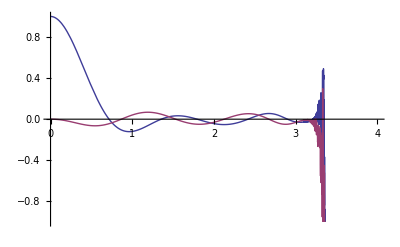

```mathematica
Ge={Re[#],Im[#]}&[Un[En,2,250,x][[1]]];Plot[Ge,{x,0,4},PlotRange->{-1,1}]
```